# QVSA Strength vs Ion Position

## Last Updated: 2025/08/12

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

```mathematica
(*get default plot colors*)
DefaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])];
```

## Evaluations

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## Phonon Conversion

### Coherent_C

```mathematica
(*coherent_c: convert R/B ratio to <n> assuming a coherent state*)
```

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

### Coherent_R

```mathematica
(*coherent_c: convert RSB probability ONLY to <n> assuming a coherent state*)
```

```mathematica
coherentR0={
0,9.99931658497433*^-5,0.000399890663733249,0.000899446570690410,0.00159825126849689,0.00249573182347329,0.00359115251770981,0.00488361553119066,0.00637206177417027,0.00805527186899924,0.00993186728045770,0.0120003115935124,0.0142589119372707,0.0167058205537671,0.0193390365100727,0.0221564075520917,0.0251556320982592,0.0283342613712326,0.0316897016655309,0.0352192167489441,0.0389199303954148,0.0427888290469539,0.0468227646020514,0.0510184573278918,0.0553724988935951,0.0598813555215709,0.0645413712539629,0.0693487713310517,0.0742996656783876,0.0793900524992962,0.0846158219693280,0.0899727600291077,0.0954565522719444,0.101062787922491,0.106786963902628,0.112624488980697,0.118570688000088,0.124620806183157,0.130770013506336,0.137013409142264,0.143346025964675,0.149762835111746,0.156258750603538,0.162828634009109,0.169467299158846,0.176169516897511,0.182930019873458,0.189743507359448,0.196604650100454,0.203508095183842,0.210448470927264,0.217420391779606,0.224418463230326,0.231437286722481,0.238471464564783,0.245515604837990,0.252564326290965,0.259612263221736,0.266654070338924,0.273684427598902,0.280698045014097,0.287689667427855,0.294654079251349,0.301586109158018,0.308480634731091,0.315332587059793,0.322136955279870,0.328888791054132,0.335583212988793,0.342215410981400,0.348780650496278,0.355274276763424,0.361691718896910,0.368028493928910,0.374280210755539,0.380442573990817,0.386511387725119,0.392482559184592,0.398352102288109,0.404116141098438,0.409770913164383,0.415312772750811,0.420738193953524,0.426043773696107,0.431226234605960,0.436282427766861,0.441209335345508,0.446004073089648,0.450663892695473,0.455186184042142,0.459568477291385,0.463808444850291,0.467903903195516,0.471852814557270,0.475653288461590,0.479303583129547,0.482802106732168,0.486147418499979,0.489338229686260,0.492373404383192,0.495251960190268,0.497973068734440,0.500536056041652,0.502940402759546,0.505185744231242,0.507271870420298,0.509198725687029,0.510966408416576,0.512575170499202,0.514025416663485,0.515317703663170,0.516452739318639,0.517431381414049,0.518254636451358,0.518923658262584,0.519439746481792,0.519804344878417,0.520019039553689,0.520085557002049,0.520005762039560,0.519781655601477,0.519415372411236,0.518909178523259,0.518265468742100,0.517486763920557,0.516575708139507,0.515535065772334,0.514367718436921,0.513076661838286,0.511665002505056,0.510135954423077,0.508492835569525,0.506739064351023,0.504878155949329,0.502913718578252,0.500849449655556,0.498689131893661,0.496436629313061,0.494095883182420,0.491670907889407,0.489165786746364,0.486584667734993,0.483931759194270,0.481211325455891,0.478427682431564,0.475585193156511,0.472688263293616,0.469741336602651,0.466748890379059,0.463715430866808,0.460645488649837,0.457543614026645,0.454414372372584,0.451262339494410,0.448092096981688,0.444908227559604,0.441715310447763,0.438517916729525,0.435320604736432,0.432127915452247,0.428944367941117,0.425774454804329,0.422622637670119,0.419493342720928,0.416390956262505,0.413319820339149,0.410284228399400,0.407288421016389,0.404336581667029,0.401432832574140,0.398581230615570,0.395785763304283,0.393050344843310,0.390378812259402,0.387774921619125,0.385242344331059,0.382784663537692,0.380405370600468,0.378107861681413,0.375895434424601,0.373771284740682,0.371738503697539,0.369800074520074,0.367958869701985,0.366217648232303,0.364579052939329,0.363045607954507,0.361619716298632,0.360303657592692,0.359099585895489,0.358009527670097,0.357035379881037,0.356178908223974,0.355441745489547,0.354825390062886,0.354331204560147,0.353960414603333,0.353714107734502,0.353593232470306,0.353598597497709,0.353730871011554};
```

```mathematica
coherentRX0=Range[0.,2.,2./(Length[coherentR0]-1)]^2.;
```

```mathematica
(*note: need to truncate after 120 points b/c curve is non-injective after that*)
CoherentRFunc=Interpolation[Transpose[{coherentR0,coherentRX0}][[;;120]]];
CoherentR[x_]:=CoherentRFunc[#]&[Clip[x,{0.,0.6}]];
```

### Coherent_ARP

```mathematica
(*todo: account for n != 0*)
CoherentARP[P_,n_:0]:=-Log[P+1.*^-7];
```

### QVSA Special Scale

```mathematica
(*extract scaled phonon number from parameters*)
fdj[att_,ampl_,nbar_]:=√(nbar/((ampl*10.^((31.5-att)/20.))^4.));
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

# 2025/08/02 - 2025/08/03: QVSA Null - Axial

## Data Store

```mathematica
(*(*2025/08/02 - 2025/08/03 - proof of concept*)
(*{
{ion_pos_x, ion_pos_y}, {volt_east_endcap, volt_west_endcap},
 {att_axial, ampl_axial, nbar_axial},{att_RF, ampl_RF, nbar_RF},{att_EGGS, ampl_EGGS, nbar_EGGS}
}*)
dataDJ={
{{224,327},{182,343},{31.5,25.,0.462},{31.5,8.,0.533},{31.5,2.,0.487}},
{{237,327},{188,332},{31.5,28.,0.534},{31.5,8.,0.572},{31.5,2.,0.510}},
{{257,328},{198,317},{31.5,40.,1.135},{31.5,8.,0.593},{31.5,2.,0.580}},
{{270,328},{205,308},{31.5,40.,0.575},{31.5,8.,0.497},{31.5,2.,0.552}},
{{274,329},{207,305},{31.5,40.,0.566},{31.5,8.,0.504},{31.5,2.,0.543}},
{{282,329},{211,299},{31.5,40.,0.332},{31.5,8.,0.512},{31.5,2.,0.521}},
{{294,329},{217,290},{31.5,40.,0.140},{31.5,8.,0.490},{31.5,2.,0.449}},
{{313,330},{227,275},{20.,40.,0.383},{31.5,8.,0.502},{31.5,2.,0.526}},
{{338,331},{243,261},{29.,40.,0.599},{31.5,8.,0.431},{31.5,2.,0.457}},
{{349,332},{250,254},{31.,40.,0.512},{31.5,8.,0.381},{31.5,2.,0.367}}
};*)
```

```mathematica
(*(*data select*)
(*2025/08/04 - binary search axial qvsa null*)
(*{
{ion_pos_x, ion_pos_y}, {volt_east_endcap, volt_west_endcap},
 {att_axial, ampl_axial, nbar_axial},{att_RF, ampl_RF, nbar_RF},{att_EGGS, ampl_EGGS, nbar_EGGS}
}*)
dataDJ={
{{303,331},{223,284},{28.,40.,0.445},{31.5,8.,0.502},{31.5,2.,0.526}},
{{313,331},{229,277},{22.,40.,0.541},{31.5,8.,0.502},{31.5,2.,0.526}},
{{315,331},{230,275},{18.,40.,0.601},{31.5,8.,0.502},{31.5,2.,0.526}},
{{316,331},{231,275},{18.,40.,0.494},{31.5,8.,0.502},{31.5,2.,0.526}},
{{317,331},{231,274},{17.5,40.,0.555},{31.5,8.,0.502},{31.5,2.,0.526}},
{{318,331},{232,274},{19.,43.,0.555},{31.5,8.,0.502},{31.5,2.,0.526}},
{{323,331},{237,270},{24.,40.,0.529},{31.5,8.,0.502},{31.5,2.,0.526}}
};*)
```

## Data Select

```mathematica
(*2025/08/02 - 2025/08/03 - proof of concept*)
dataDJ={
{{224,327},{182,343},{31.5,25.,0.462},{31.5,8.,0.533},{31.5,2.,0.487}},
{{237,327},{188,332},{31.5,28.,0.534},{31.5,8.,0.572},{31.5,2.,0.510}},
{{257,328},{198,317},{31.5,40.,1.135},{31.5,8.,0.593},{31.5,2.,0.580}},
{{270,328},{205,308},{31.5,40.,0.575},{31.5,8.,0.497},{31.5,2.,0.552}},
{{274,329},{207,305},{31.5,40.,0.566},{31.5,8.,0.504},{31.5,2.,0.543}},
{{282,329},{211,299},{31.5,40.,0.332},{31.5,8.,0.512},{31.5,2.,0.521}},
{{294,329},{217,290},{31.5,40.,0.140},{31.5,8.,0.490},{31.5,2.,0.449}},
{{313,330},{227,275},{20.,40.,0.383},{31.5,8.,0.502},{31.5,2.,0.526}},
{{338,331},{243,261},{29.,40.,0.599},{31.5,8.,0.431},{31.5,2.,0.457}},
{{349,332},{250,254},{31.,40.,0.512},{31.5,8.,0.381},{31.5,2.,0.367}}
};
```

## Process

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[1,1]]<#2[[1,1]]&];
posDJ=dataDJ[[;;,1,1]];
```

```mathematica
(*process axial*)
dataDJAx={dataDJ[[;;,3,{1,2}]],dataDJ[[;;,3,3]]};
voltDJAx=(#2*10.^((31.5-#1)/20.))&@@@dataDJAx[[1]];
κDJAx=√(dataDJAx[[2]]/voltDJAx^4);κDJAx/=Min[κDJAx];
dataPlotDJAx=Transpose[{posDJ,κDJAx}];
```

```mathematica
(*process RF*)
dataDJRF={dataDJ[[;;,4,{1,2}]],dataDJ[[;;,4,3]]};
voltDJRF=(#2*10.^((31.5-#1)/20.))&@@@dataDJRF[[1]];
κDJRF=√(dataDJRF[[2]]/voltDJRF^4);κDJRF/=Min[κDJRF];
dataPlotDJRF=Transpose[{posDJ,κDJRF}];
```

```mathematica
(*process EGGS*)
dataDJEGGS={dataDJ[[;;,5,{1,2}]],dataDJ[[;;,5,3]]};
voltDJEGGS=(#2*10.^((31.5-#1)/20.))&@@@dataDJEGGS[[1]];
κDJEGGS=√(dataDJEGGS[[2]]/voltDJEGGS^4);κDJEGGS/=Min[κDJEGGS];
dataPlotDJEGGS=Transpose[{posDJ,κDJEGGS}];
```

## Try Fit

```mathematica
dataPlotDJAx
```

{{224,39.7156},{237,34.0389},{257,24.3164},{270,17.3075},{274,17.1715},{282,13.1513},{294,8.54013},{313,1.},{338,9.93377},{349,14.5558}}

```mathematica
(*fit function*)
fitfunc=Ampl*Abs[x-x0]+C0;
fitConstraintsDJ={Ampl>0.,C0>0.};
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[dataPlotDJAx[[First/@{Ordering[dataPlotDJAx[[;;,2]],-1],Ordering[dataPlotDJAx[[;;,2]],1]}]]]},
{x0,First@dataPlotDJAx[[Ordering[dataPlotDJAx[[;;,2]],1],1]]},
{C0,Min[dataPlotDJAx[[;;,2]]]}
}
```

{{Ampl,0.435007},{x0,313},{C0,1.}}

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[dataPlotDJAx,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
];
]
```

{0.0071007,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dataPlotDJAx[[1,1]],dataPlotDJAx[[-1,1]]}
];
```

```mathematica
(*plot raw data*)
summaryFigure=Show[{
ListPlot[
{
dataPlotDJAx,dataPlotDJAx
(*dataPlotDJRF,dataPlotDJRF,
dataPlotDJEGGS,dataPlotDJEGGS*)
},

PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["QVSA Strength vs Axial Position",{Black,Directive[15]}]
}
},
PlotStyle->{
{Black,PointSize[0.01]},
{Black,Dashed,Thickness[0.003]},
{Green,PointSize[0.01]},
{Green,Dashed,Thickness[0.003]},
{Red,PointSize[0.01]},
{Red,Dashed,Thickness[0.003]}
},
Joined->{
False,True,
False,True,
False,True
},
PlotLegends->{"Axial",None,"RF",None,"EGGS",None},

ImageSize->Scaled[0.5]
],

(*combine with fitted plot*)
fitPlot
}];
```

## Show

| Estimate | Standard Error | Confidence Interval
Ampl | 0.430416 | 0.0114792 | {0.403272,0.457559}
x0 | 314.178 | 0.844564 | {312.181,316.175}
C0 | 2.15949×10^-7 | 0.554242 | {-1.31057,1.31057}

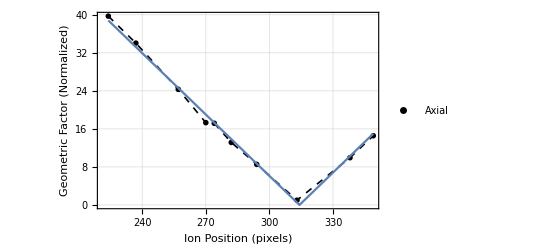

```mathematica
fitParams
summaryFigure
```

# 2025/08/04: Axial xum null (Josh)

## Dadadada

# 2025/08/07 - 2025/08/09: QVSA CH1 Silliness vs Position (Axial)

## Dadadada

## Data Store

Dataset Structure: {
	{ion_pos_x,ion_pos_y},{volt_east_endcap, volt_west_endcap}, {xum_rabi_ratio},
	{att_axial_raw, ampl_axial_raw, nbar_axial_raw},
	{att_axial _ch0, ampl_axial_ch0, nbar_axial_ch0},  {att_axial_ch1, ampl_axial_ch1, nbar_axial_ch1},
	{phas_osc0, phas_osc1},
}

2025/08/07: qvsa strength + CH1 phase/ampl imbal; after warmup

```mathematica
(*(*2025/08/07: qvsa strength + CH1 phase/ampl imbal; after warmup*)
dataDJ={
{{283,336},{205,308},{1./22.50},{30.,40.,0.529},{22.,40.,0.682},{22.,22.5,0.530},{-0.0662,-0.2488}},{{330,337},{231,275},{1./8.18},{26.,40.,0.738},{19.,20.,0.655},{19.,40.,0.539},{-0.0843,-0.0493}},
{{351,339},{243,261},{1./5.05},{31.5,40.,0.519},{22.,22.,0.681},{22.,40.,0.622},{-0.0386,-0.1186}}
};*)
```

2025/08/08: qvsa strength + CH1 phase/ampl imbal; after warmup

```mathematica
(*(*2025/08/08: qvsa strength + CH1 phase/ampl imbal; after warmup*)
dataDJ={
{{238,335},{182,343},{1./13.43},{31.5,30.,0.836},{26.,34.,0.575},{26.,24.,0.502},{-0.0936,-0.1158}},
{{282,337},{205,308},{1./14.84},{31.5,40.,0.495},{22.,43.,0.529},{22.,20.,0.526},{-0.0690,-0.1485}},
{{283,336},{205,308},{1./22.50},{30.,40.,0.529},{22.,40.,0.682},{22.,22.5,0.530},{-0.0662,-0.2488}},
{{306,337},{217,290},{1./10.90},{26.5,40.,0.664},{20.,45.,0.833},{20.,22.,0.771},{0.2743,0.4412}},
{{330,337},{231,275},{1./8.18},{26.,40.,0.738},{19.,20.,0.655},{19.,40.,0.539},{-0.0843,-0.0493}},
{{351,339},{243,261},{1./5.05},{31.5,40.,0.519},{22.,22.,0.681},{22.,40.,0.622},{-0.0386,-0.1186}},
{{362,339},{250,254},{1./4.96},{31.5,40.,0.691},{22.,20.,0.555},{22.,35.,0.537},{-0.0843,-0.0806}}
};*)
```

## Data Select

```mathematica
(*collate dataset du jour*)
dataDJ={
{{238,335},{182,343},{1./13.43},{31.5,30.,0.836},{26.,34.,0.575},{26.,24.,0.502},{-0.0936,-0.1158}},
{{255,335},{190,330},{1./24.39},{31.5,30.,0.455},{25.,35.,0.508},{25.,25.,0.656},{-0.1022,-0.1329}},
{{282,337},{205,308},{1./14.84},{31.5,40.,0.495},{22.,43.,0.529},{22.,20.,0.526},{-0.0690,-0.1485}},
{{283,336},{205,308},{1./22.50},{30.,40.,0.529},{22.,40.,0.682},{22.,22.5,0.530},{-0.0662,-0.2488}},
{{306,337},{217,290},{1./10.90},{26.5,40.,0.664},{20.,45.,0.833},{20.,22.,0.771},{0.2743,0.4412}},
{{319,338},{224,282},{1./13.17},{17.,40.,0.484},{23.,40.,0.579},{23.,36.,0.595},{0.2743,0.4412}},
{{330,337},{231,275},{1./8.18},{26.,40.,0.738},{19.,20.,0.655},{19.,40.,0.539},{-0.0843,-0.0493}},
{{351,339},{243,261},{1./5.05},{31.5,40.,0.519},{22.,22.,0.681},{22.,40.,0.622},{-0.0386,-0.1186}},
{{362,339},{250,254},{1./4.96},{31.5,40.,0.691},{22.,20.,0.555},{22.,35.,0.537},{-0.0843,-0.0806}},
{{383,340},{263,242},{1./3.95},{31.5,32.,0.578},{26.,29.,0.722},{26.,40.,0.571},{-0.1018,-0.1364}}
};
```

## Process

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[1,1]]<#2[[1,1]]&];
posDJ=dataDJ[[;;,1,1]];
```

```mathematica
(*convert phonon/QVSA params to scaled voltage*)
phononDataDJ=Apply[
fdj,
dataDJ[[;;,{4,5,6}]],
{2}
]//Transpose;
```

```mathematica
(*process QVSA strength data*)
dataQVSANull=Transpose[{posDJ,phononDataDJ[[1]]}];
dataQVSANull[[;;,2]]/=Min[dataQVSANull[[;;,2]]];
```

```mathematica
(*process xum null data*)
dataXUMNull=Transpose[{posDJ,dataDJ[[;;,3,1]]}];
(*dataXUMNull[[;;,2]]/=Min[dataXUMNull[[;;,2]]];*)
(*dataXUMNull[[;;,2]]-=Min[dataXUMNull[[;;,2]]];
dataXUMNull[[;;,2]]*=20.;*)
```

```mathematica
(*process CH0 vs CH1 ampl imbalance data*)
dataCH0Ampl=Transpose[{posDJ,phononDataDJ[[2]]}];
dataCH1Ampl=Transpose[{posDJ,phononDataDJ[[3]]}];
(*normalize to minimum of BOTH CH0 and CH1 vals instead of respectively*)
amplImbalanceNorm=Min[phononDataDJ[[2;;3]]];
dataCH0Ampl[[;;,2]]/=amplImbalanceNorm;
dataCH1Ampl[[;;,2]]/=amplImbalanceNorm;
```

```mathematica
(*process osc phases*)
dataOsc0Phase=Transpose[{posDJ,dataDJ[[;;,7,1]]}];
dataOsc1Phase=Transpose[{posDJ,dataDJ[[;;,7,2]]}];
(*(*normalize to minimum of BOTH CH0 and CH1 vals instead of respectively*)
amplImbalanceNorm=Min[phononDataDJ[[2;;3]]];
dataCH0Strength[[;;,2]]/=amplImbalanceNorm;
dataCH1Strength[[;;,2]]/=amplImbalanceNorm;*)
```

## Try Fit

## Prepare Fitting

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
];
]];
```

## Do Fits

```mathematica
(*fit QVSA field null to abs func*)
AbsoluteTiming[
fitQVSANull=FitAbsFunc[dataQVSANull];
];
```

```mathematica
(*fit micromotion null to abs func*)
AbsoluteTiming[
fitXUMNull=FitAbsFunc[dataXUMNull];
];
```

```mathematica
(*fit CH0/CH1 relative geometric factor to abs func*)
AbsoluteTiming[
fitCH0Ampl=FitAbsFunc[dataCH0Ampl];
fitCH1Ampl=FitAbsFunc[dataCH1Ampl];
];
```

## Get Fit Params

```mathematica
(*get fit params*)
fitQVSAParams=Style[
fitQVSANull["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitXUMParams=Style[
fitXUMNull["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0Params=Style[
fitCH0Ampl["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1Params=Style[
fitCH1Ampl["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

## QVSA Null

```mathematica
(*plot fitted results*)
fitQVSAPlot=Plot[
fitQVSANull[x],
{x,dataQVSANull[[1,1]],dataQVSANull[[-1,1]]},
PlotStyle->{DefaultPlotColors[[1]],Thickness[0.0033],Opacity[0.85]}
];
```

```mathematica
(*plot qvsa null data*)
summaryQVSAFigure=Show[{
ListPlot[
{dataQVSANull,dataQVSANull},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["QVSA Field Null (Axial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.018]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True,
False,True
},
PlotLegends->{"Raw QVSA Strength",None},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitQVSAPlot
}];
```

## Trap XUM Null

```mathematica
(*plot fitted results*)
fitXUMPlot=Plot[
fitXUMNull[x],
{x,dataXUMNull[[1,1]],dataXUMNull[[-1,1]]},
PlotStyle->{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
];
```

```mathematica
(*plot trap xum null data*)
summaryXUMFigure=Show[{
ListPlot[
{dataXUMNull,dataXUMNull},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Micromotion Index (β)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["Trap RF Field Null (Axial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True,
False,True
},
PlotLegends->{"XUM Null",None},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitXUMPlot
}];
```

## CH0 vs CH1 “Geometric Factor”

```mathematica
(*plot fitted results*)
fitCH0Plot=Plot[
fitCH0Ampl[x],
{x,dataCH0Ampl[[1,1]],dataCH0Ampl[[-1,1]]},
PlotStyle->{DefaultPlotColors[[3]],Thickness[0.0033],Opacity[0.85]}
];
fitCH1Plot=Plot[
fitCH1Ampl[x],
{x,dataCH1Ampl[[1,1]],dataCH1Ampl[[-1,1]]},
PlotStyle->{DefaultPlotColors[[4]],Thickness[0.0033],Opacity[0.85]}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1Figure=Show[{
ListPlot[
{
dataCH0Ampl,dataCH0Ampl,
dataCH1Ampl,dataCH1Ampl
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[3]],PointSize[0.018]},
{DefaultPlotColors[[3]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[4]],PointSize[0.018]},
{DefaultPlotColors[[4]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{"CH0",None,"CH1",None},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitCH0Plot,
fitCH1Plot
}];
```

## CH1 Phase per osc

```mathematica
(*plot osc phase data*)
summaryOscPhaseFigure=Show[{
ListPlot[
{
dataOsc0Phase,dataOsc0Phase,
dataOsc1Phase,dataOsc1Phase
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["CH1 Phase (turns)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["Relative CH1 Phase (by Oscillator)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[3]],PointSize[0.018]},
{DefaultPlotColors[[3]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[4]],PointSize[0.018]},
{DefaultPlotColors[[4]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{"osc0 (BSB)",None,"osc1 (Carrier)",None},

ImageSize->Scaled[0.31]
]

(*combine with fitted plot*)
(*todo*)
}];
```

## Show

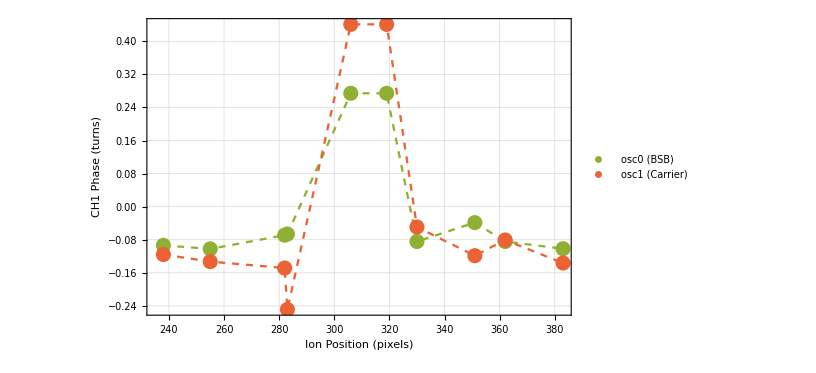

```mathematica
summaryOscPhaseFigure
```

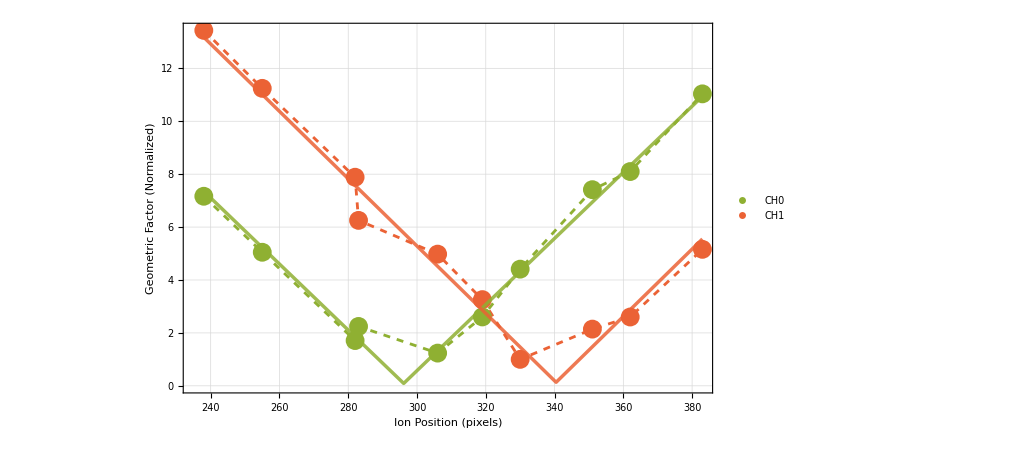
( | Estimate | Standard Error | Confidence Interval
Ampl | 0.124917 | 0.00442467 | {0.114455,0.13538}
x0 | 296.131 | 0.888982 | {294.029,298.233}
C0 | 0.0906338 | 0.201578 | {-0.386022,0.56729}
 | Estimate | Standard Error | Confidence Interval
Ampl | 0.127301 | 0.00756817 | {0.109405,0.145197}
x0 | 340.449 | 1.93209 | {335.88,345.017}
C0 | 0.133203 | 0.368595 | {-0.738385,1.00479}
-Graphics-)

```mathematica
{{fitCH0Params,fitCH1Params,summaryCH0CH1Figure}}//Transpose//MatrixForm
```

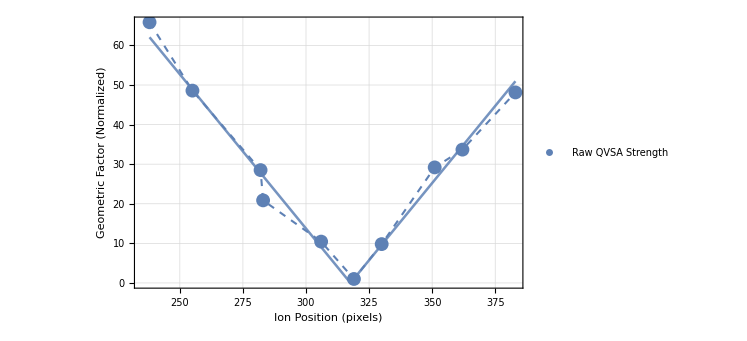
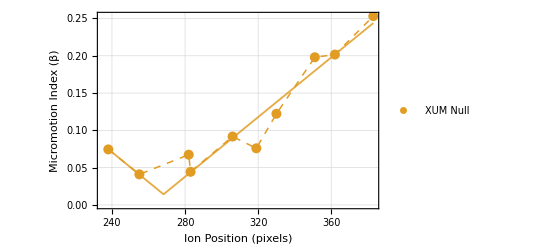
( | Estimate | Standard Error | Confidence Interval
Ampl | 0.779392 | 0.044011 | {0.675323,0.883461}
x0 | 317.628 | 1.36713 | {314.395,320.861}
C0 | 8.94672×10^-7 | 1.96453 | {-4.64538,4.64538} |  | Estimate | Standard Error | Confidence Interval
Ampl | 0.00200019 | 0.000208571 | {0.001507,0.00249339}
x0 | 268.23 | 4.46828 | {257.664,278.796}
C0 | 0.0142677 | 0.0116375 | {-0.0132507,0.0417861}
-Graphics- | -Graphics-)

```mathematica
{
{fitQVSAParams,summaryQVSAFigure},
{fitXUMParams,summaryXUMFigure}
}//Transpose//MatrixForm
```

# 2025/08/12: QVSA Null - H Shim

## Dadadada

## Data Store

Dataset Structure: {
	{ion_pos_x, ion_pos_y}, {volt_vertical_shim, volt_horizontal_shim},
	{att_RF_raw, ampl_RF_raw, nbar_RF_raw}, {att_RF_ch0, ampl_RF_ch0, nbar_RF_ch0},  {att_RF_ch1, ampl_RF_ch1, nbar_RF_ch1},
	{att_EGGS_raw, ampl_EGGS_raw, nbar_EGGS_raw}, {att_EGGS_ch0, ampl_EGGS_ch0, nbar_EGGS_ch0},  {att_EGGS_ch1, ampl_EGGS_ch1, nbar_EGGS_ch1}
}

2025/08/12: qvsa strength (radial) at different radial positions - adjust H shim only (b/c visible on camera)

```mathematica
(*2025/08/12: qvsa strength + CH1 phase/ampl imbal; after warmup*)
dataDJ={
{
{279,337},{72.7,5.},
{{31.5,3.,0.761},{31.5,4.3,0.481},{31.5,3.5,0.607}},
{{31.5,10.,0.609},{25.,8.,0.311},{25.,10.,0.534}}
},
{
{279,333},{72.7,20.}, 
{{31.5,3.,0.863},{31.5,4.3,0.548},{31.5,3.5,0.588}},
{{31.5,10.,0.574},{25.,9.,0.530},{25.,8.,0.720}}
},
{
{281,337},{72.7,35.},
{{31.5,3.,0.803},{31.5,4.3,0.531},{31.5,3.5,0.700}},
{{31.5,10.,0.568},{25.,12.,0.860},{25.,8.,0.444}}
},
{
{279,336},{72.7,45.},
{{31.5,3.,0.795},{31.5,4.3,0.529},{31.5,3.5,0.692}},
{{31.5,10.,0.525},{25.,12.,0.562},{25.,8.,0.485}}
},
{
{280,336},{72.7,51.7},
{{31.5,3.,0.708},{31.5,4.7,0.766},{31.5,3.8,0.766}},
{{31.5,10.5,0.583},{31.5,29.0,0.609},{31.5,17.,0.555}}
},
{
{279,336},{72.7,55.7},
{{31.5,3.,0.806},{31.5,4.7,0.759},{31.5,3.8,0.912}},
{{31.5,12.,1.023},{31.5,29.,0.508},{31.5,17.,0.588}}
},
{
{280,335},{72.7,59.7},
{{31.5,3.,0.780},{31.5,4.7,0.652},{31.5,3.8,0.871}},
{{31.5,11.,0.598},{31.5,35.,0.617},{31.5,17.,0.633}}
},
{
{280,335},{72.7,63.7},
{{31.5,3.,0.820},{31.5,4.7,0.609},{31.5,3.8,0.973}},
{{31.5,11.,0.667},{31.5,35.,0.400},{31.5,17.,0.655}}
},
{
{280,335},{72.7,67.7},
{{31.5,3.,0.742},{31.5,4.7,0.672},{31.5,3.8,0.946}},
{{31.5,11.,0.705},{31.5,40.,0.498},{31.5,17.,0.636}}
},
{
{279,335},{72.7,71.7},
{{31.5,3.,0.880},{31.5,4.7,0.792},{31.5,3.8,0.895}},
{{31.5,11.,0.685},{25.,25.,0.800},{25.,8.,0.699}}
},
{
{279,334},{72.7,78.7},
{{31.5,3.,0.718},{31.5,4.3,0.619},{31.5,3.5,0.566}},
{{31.5,11.,0.639},{25.,25.,0.566},{25.,8.,0.772}}
},
{
{279,333},{72.7,88.8},
{{31.5,3.,0.769},{31.5,4.3,0.476},{31.5,3.5,0.615}},
{{31.5,11.,0.613},{25.,25.,0.647},{25.,8.,0.781}}
}
};
```

## Data Select

```mathematica
(*collate dataset du jour*)
(*2025/08/12: radial qvsa strength vs V Shim*)
dataDJ={
{
{279,337},{72.7,5.},
{{31.5,3.,0.761},{31.5,4.3,0.481},{31.5,3.5,0.607}},
{{31.5,10.,0.609},{25.,8.,0.311},{25.,10.,0.534}}
},
{
{279,333},{72.7,20.}, 
{{31.5,3.,0.863},{31.5,4.3,0.548},{31.5,3.5,0.588}},
{{31.5,10.,0.574},{25.,9.,0.530},{25.,8.,0.720}}
},
{
{281,337},{72.7,35.},
{{31.5,3.,0.803},{31.5,4.3,0.531},{31.5,3.5,0.700}},
{{31.5,10.,0.568},{25.,12.,0.860},{25.,8.,0.444}}
},
{
{279,336},{72.7,45.},
{{31.5,3.,0.795},{31.5,4.3,0.529},{31.5,3.5,0.692}},
{{31.5,10.,0.525},{25.,12.,0.562},{25.,8.,0.485}}
},
{
{280,336},{72.7,51.7},
{{31.5,3.,0.708},{31.5,4.7,0.766},{31.5,3.8,0.766}},
{{31.5,10.5,0.583},{31.5,29.0,0.609},{31.5,17.,0.555}}
},
{
{279,336},{72.7,55.7},
{{31.5,3.,0.806},{31.5,4.7,0.759},{31.5,3.8,0.912}},
{{31.5,12.,1.023},{31.5,29.,0.508},{31.5,17.,0.588}}
},
{
{280,335},{72.7,59.7},
{{31.5,3.,0.780},{31.5,4.7,0.652},{31.5,3.8,0.871}},
{{31.5,11.,0.598},{31.5,35.,0.617},{31.5,17.,0.633}}
},
{
{280,335},{72.7,63.7},
{{31.5,3.,0.820},{31.5,4.7,0.609},{31.5,3.8,0.973}},
{{31.5,11.,0.667},{31.5,35.,0.400},{31.5,17.,0.655}}
},
{
{280,335},{72.7,67.7},
{{31.5,3.,0.742},{31.5,4.7,0.672},{31.5,3.8,0.946}},
{{31.5,11.,0.705},{31.5,40.,0.498},{31.5,17.,0.636}}
},
{
{279,335},{72.7,71.7},
{{31.5,3.,0.880},{31.5,4.7,0.792},{31.5,3.8,0.895}},
{{31.5,11.,0.685},{25.,25.,0.800},{25.,8.,0.699}}
},
{
{279,334},{72.7,78.7},
{{31.5,3.,0.718},{31.5,4.3,0.619},{31.5,3.5,0.566}},
{{31.5,11.,0.639},{25.,25.,0.566},{25.,8.,0.772}}
},
{
{279,333},{72.7,88.8},
{{31.5,3.,0.769},{31.5,4.3,0.476},{31.5,3.5,0.615}},
{{31.5,11.,0.613},{25.,25.,0.647},{25.,8.,0.781}}
}
};
```

## Process

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[2,2]]<#2[[2,2]]&];
posDJ=dataDJ[[;;,2,2]];
```

```mathematica
(*convert phonon/QVSA params to scaled voltage*)
phononDataDJEGGS=Apply[
fdj,
dataDJ[[;;,3,;;]],
{2}
]//Transpose;
phononDataDJRF=Apply[
fdj,
dataDJ[[;;,4,;;]],
{2}
]//Transpose;
```

```mathematica
(*process QVSA strength data*)
dataQVSANullEGGS=Transpose[{posDJ,phononDataDJEGGS[[1]]}];
dataQVSANullEGGS[[;;,2]]/=Min[dataQVSANullEGGS[[;;,2]]];
dataQVSANullRF=Transpose[{posDJ,phononDataDJRF[[1]]}];
dataQVSANullRF[[;;,2]]/=Min[dataQVSANullRF[[;;,2]]];
```

```mathematica
(*process CH0 vs CH1 ampl imbalance data*)
dataCH0AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[2]]}];
dataCH1AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[3]]}];
dataCH0AmplRF=Transpose[{posDJ,phononDataDJRF[[2]]}];
dataCH1AmplRF=Transpose[{posDJ,phononDataDJRF[[3]]}];
```

```mathematica
(*normalize to minimum of BOTH CH0 and CH1 vals instead of respectively*)
(*amplImbalanceNorm=Min[{phononDataDJEGGS[[2;;3]],phononDataDJRF[[2;;3]]}];*)
amplImbalanceNormEGGS=Min[phononDataDJEGGS[[2;;3]]];
amplImbalanceNormRF=Min[phononDataDJRF[[2;;3]]];
dataCH0AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH1AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH0AmplRF[[;;,2]]/=amplImbalanceNormRF;
dataCH1AmplRF[[;;,2]]/=amplImbalanceNormRF;
```

## Try Fit

## Prepare Fitting

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
];
]];
```

## Do Fits

```mathematica
(*fit QVSA field null to abs func*)
AbsoluteTiming[
fitQVSANullEGGS=FitAbsFunc[dataQVSANullEGGS];
]
AbsoluteTiming[
fitQVSANullRF=FitAbsFunc[dataQVSANullRF];
]
```

{0.107395,Null}

{0.0067753,Null}

```mathematica
(*fit CH0/CH1 relative geometric factor to abs func*)
AbsoluteTiming[
fitCH0AmplEGGS=FitAbsFunc[dataCH0AmplEGGS];
fitCH1AmplEGGS=FitAbsFunc[dataCH1AmplEGGS];
]
AbsoluteTiming[
fitCH0AmplRF=FitAbsFunc[dataCH0AmplRF];
fitCH1AmplRF=FitAbsFunc[dataCH1AmplRF];
]
```

{0.15111,Null}

{0.0154849,Null}

## Get Fit Params

```mathematica
(*get fit params*)
fitQVSAParamsEGGS=Style[
fitQVSANullEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitQVSAParamsRF=Style[
fitQVSANullRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsEGGS=Style[
fitCH0AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsEGGS=Style[
fitCH1AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsRF=Style[
fitCH0AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsRF=Style[
fitCH1AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

## QVSA Null

```mathematica
(*plot fitted results*)
fitQVSAPlot=Plot[
{fitQVSANullEGGS[x],fitQVSANullRF[x]},
{x,dataQVSANullRF[[1,1]],dataQVSANullRF[[-1,1]]},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.0033],Opacity[0.85]},
{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot qvsa null data*)
summaryQVSAFigure=Show[{
ListPlot[
{
dataQVSANullEGGS,dataQVSANullEGGS,
dataQVSANullRF,dataQVSANullRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["QVSA Field Null (Radial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.018]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},

PlotLegends->{
"Uncompensated - EGGS",None,
"Uncompensated - RF",None
},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitQVSAPlot
}];
```

## CH0 vs CH1 “Geometric Factor”

### EGGS mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotEGGS=Plot[
fitCH0AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[3]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotEGGS=Plot[
fitCH1AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[4]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureEGGS=Show[{
ListPlot[
{
dataCH0AmplEGGS,dataCH0AmplEGGS,
dataCH1AmplEGGS,dataCH1AmplEGGS
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[3]],PointSize[0.018]},
{DefaultPlotColors[[3]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[4]],PointSize[0.018]},
{DefaultPlotColors[[4]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - EGGS",None,
"CH1 - EGGS",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotEGGS,
fitCH1PlotEGGS
}];
```

### RF Mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotRF=Plot[
fitCH0AmplRF[x],
{x,dataCH0AmplRF[[1,1]],dataCH0AmplRF[[-1,1]]},
PlotStyle->{
DefaultPlotColors[[5]],Thickness[0.0033],Opacity[0.85]
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotRF=Plot[
fitCH1AmplRF[x],
{x,dataCH1AmplRF[[1,1]],dataCH1AmplRF[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[6]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureRF=Show[{
ListPlot[
{
dataCH0AmplRF,dataCH0AmplRF,
dataCH1AmplRF,dataCH1AmplRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[5]],PointSize[0.018]},
{DefaultPlotColors[[5]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[6]],PointSize[0.018]},
{DefaultPlotColors[[6]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - RF",None,
"CH1 - RF",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotRF,
fitCH1PlotRF
}];
```

## Show

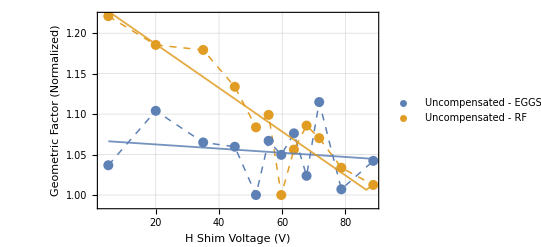

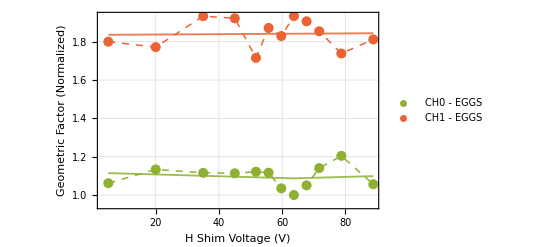
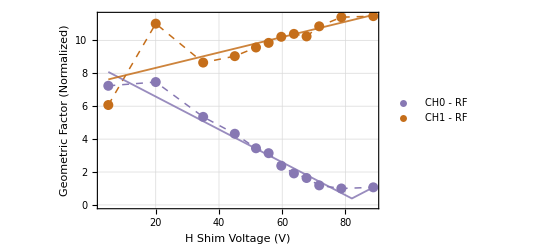
(-Graphics-
-Graphics-)

```mathematica
summaryQVSAFigure
Transpose[{summaryCH0CH1FigureEGGS,summaryCH0CH1FigureRF}]//MatrixForm
```

# 2025/08/12: QVSA Null - V Shim (***todo***)

## Dadadada

## Data Store

Dataset Structure: {
	{ion_pos_x, ion_pos_y}, {volt_vertical_shim, volt_horizontal_shim},
	{att_RF_raw, ampl_RF_raw, nbar_RF_raw}, {att_RF_ch0, ampl_RF_ch0, nbar_RF_ch0},  {att_RF_ch1, ampl_RF_ch1, nbar_RF_ch1},
	{att_EGGS_raw, ampl_EGGS_raw, nbar_EGGS_raw}, {att_EGGS_ch0, ampl_EGGS_ch0, nbar_EGGS_ch0},  {att_EGGS_ch1, ampl_EGGS_ch1, nbar_EGGS_ch1}
}

2025/08/12: qvsa strength (radial) at different radial positions - adjust H shim only (b/c visible on camera)

```mathematica
(*2025/08/12: qvsa strength + CH1 phase/ampl imbal; after warmup*)
dataDJ={
{
{279,337},{72.7,5.},
{{31.5,3.,0.761},{31.5,4.3,0.481},{31.5,3.5,0.607}},
{{31.5,10.,0.609},{25.,8.,0.311},{25.,10.,0.534}}
},
{
{279,333},{72.7,20.}, 
{{31.5,3.,0.863},{31.5,4.3,0.548},{31.5,3.5,0.588}},
{{31.5,10.,0.574},{25.,9.,0.530},{25.,8.,0.720}}
},
{
{281,337},{72.7,35.},
{{31.5,3.,0.803},{31.5,4.3,0.531},{31.5,3.5,0.700}},
{{31.5,10.,0.568},{25.,12.,0.860},{25.,8.,0.444}}
},
{
{279,336},{72.7,45.},
{{31.5,3.,0.795},{31.5,4.3,0.529},{31.5,3.5,0.692}},
{{31.5,10.,0.525},{25.,12.,0.562},{25.,8.,0.485}}
},
{
{280,336},{72.7,51.7},
{{31.5,3.,0.708},{31.5,4.7,0.766},{31.5,3.8,0.766}},
{{31.5,10.5,0.583},{31.5,29.0,0.609},{31.5,17.,0.555}}
},
{
{279,336},{72.7,55.7},
{{31.5,3.,0.806},{31.5,4.7,0.759},{31.5,3.8,0.912}},
{{31.5,12.,1.023},{31.5,29.,0.508},{31.5,17.,0.588}}
},
{
{280,335},{72.7,59.7},
{{31.5,3.,0.780},{31.5,4.7,0.652},{31.5,3.8,0.871}},
{{31.5,11.,0.598},{31.5,35.,0.617},{31.5,17.,0.633}}
},
{
{280,335},{72.7,63.7},
{{31.5,3.,0.820},{31.5,4.7,0.609},{31.5,3.8,0.973}},
{{31.5,11.,0.667},{31.5,35.,0.400},{31.5,17.,0.655}}
},
{
{280,335},{72.7,67.7},
{{31.5,3.,0.742},{31.5,4.7,0.672},{31.5,3.8,0.946}},
{{31.5,11.,0.705},{31.5,40.,0.498},{31.5,17.,0.636}}
},
{
{279,335},{72.7,71.7},
{{31.5,3.,0.880},{31.5,4.7,0.792},{31.5,3.8,0.895}},
{{31.5,11.,0.685},{25.,25.,0.800},{25.,8.,0.699}}
},
{
{279,334},{72.7,78.7},
{{31.5,3.,0.718},{31.5,4.3,0.619},{31.5,3.5,0.566}},
{{31.5,11.,0.639},{25.,25.,0.566},{25.,8.,0.772}}
},
{
{279,333},{72.7,88.8},
{{31.5,3.,0.769},{31.5,4.3,0.476},{31.5,3.5,0.615}},
{{31.5,11.,0.613},{25.,25.,0.647},{25.,8.,0.781}}
}
};
```

## Data Select

```mathematica
(*collate dataset du jour*)
(*2025/08/12: radial qvsa strength vs V Shim*)
dataDJ={
{
{279,337},{72.7,5.},
{{31.5,3.,0.761},{31.5,4.3,0.481},{31.5,3.5,0.607}},
{{31.5,10.,0.609},{25.,8.,0.311},{25.,10.,0.534}}
},
{
{279,333},{72.7,20.}, 
{{31.5,3.,0.863},{31.5,4.3,0.548},{31.5,3.5,0.588}},
{{31.5,10.,0.574},{25.,9.,0.530},{25.,8.,0.720}}
},
{
{281,337},{72.7,35.},
{{31.5,3.,0.803},{31.5,4.3,0.531},{31.5,3.5,0.700}},
{{31.5,10.,0.568},{25.,12.,0.860},{25.,8.,0.444}}
},
{
{279,336},{72.7,45.},
{{31.5,3.,0.795},{31.5,4.3,0.529},{31.5,3.5,0.692}},
{{31.5,10.,0.525},{25.,12.,0.562},{25.,8.,0.485}}
},
{
{280,336},{72.7,51.7},
{{31.5,3.,0.708},{31.5,4.7,0.766},{31.5,3.8,0.766}},
{{31.5,10.5,0.583},{31.5,29.0,0.609},{31.5,17.,0.555}}
},
{
{279,336},{72.7,55.7},
{{31.5,3.,0.806},{31.5,4.7,0.759},{31.5,3.8,0.912}},
{{31.5,12.,1.023},{31.5,29.,0.508},{31.5,17.,0.588}}
},
{
{280,335},{72.7,59.7},
{{31.5,3.,0.780},{31.5,4.7,0.652},{31.5,3.8,0.871}},
{{31.5,11.,0.598},{31.5,35.,0.617},{31.5,17.,0.633}}
},
{
{280,335},{72.7,63.7},
{{31.5,3.,0.820},{31.5,4.7,0.609},{31.5,3.8,0.973}},
{{31.5,11.,0.667},{31.5,35.,0.400},{31.5,17.,0.655}}
},
{
{280,335},{72.7,67.7},
{{31.5,3.,0.742},{31.5,4.7,0.672},{31.5,3.8,0.946}},
{{31.5,11.,0.705},{31.5,40.,0.498},{31.5,17.,0.636}}
},
{
{279,335},{72.7,71.7},
{{31.5,3.,0.880},{31.5,4.7,0.792},{31.5,3.8,0.895}},
{{31.5,11.,0.685},{25.,25.,0.800},{25.,8.,0.699}}
},
{
{279,334},{72.7,78.7},
{{31.5,3.,0.718},{31.5,4.3,0.619},{31.5,3.5,0.566}},
{{31.5,11.,0.639},{25.,25.,0.566},{25.,8.,0.772}}
},
{
{279,333},{72.7,88.8},
{{31.5,3.,0.769},{31.5,4.3,0.476},{31.5,3.5,0.615}},
{{31.5,11.,0.613},{25.,25.,0.647},{25.,8.,0.781}}
}
};
```

## Process

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[2,2]]<#2[[2,2]]&];
posDJ=dataDJ[[;;,2,2]];
```

```mathematica
(*convert phonon/QVSA params to scaled voltage*)
phononDataDJEGGS=Apply[
fdj,
dataDJ[[;;,3,;;]],
{2}
]//Transpose;
phononDataDJRF=Apply[
fdj,
dataDJ[[;;,4,;;]],
{2}
]//Transpose;
```

```mathematica
(*process QVSA strength data*)
dataQVSANullEGGS=Transpose[{posDJ,phononDataDJEGGS[[1]]}];
dataQVSANullEGGS[[;;,2]]/=Min[dataQVSANullEGGS[[;;,2]]];
dataQVSANullRF=Transpose[{posDJ,phononDataDJRF[[1]]}];
dataQVSANullRF[[;;,2]]/=Min[dataQVSANullRF[[;;,2]]];
```

```mathematica
(*process CH0 vs CH1 ampl imbalance data*)
dataCH0AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[2]]}];
dataCH1AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[3]]}];
dataCH0AmplRF=Transpose[{posDJ,phononDataDJRF[[2]]}];
dataCH1AmplRF=Transpose[{posDJ,phononDataDJRF[[3]]}];
```

```mathematica
(*normalize to minimum of BOTH CH0 and CH1 vals instead of respectively*)
(*amplImbalanceNorm=Min[{phononDataDJEGGS[[2;;3]],phononDataDJRF[[2;;3]]}];*)
amplImbalanceNormEGGS=Min[phononDataDJEGGS[[2;;3]]];
amplImbalanceNormRF=Min[phononDataDJRF[[2;;3]]];
dataCH0AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH1AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH0AmplRF[[;;,2]]/=amplImbalanceNormRF;
dataCH1AmplRF[[;;,2]]/=amplImbalanceNormRF;
```

## Try Fit

## Prepare Fitting

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
];
]];
```

## Do Fits

```mathematica
(*fit QVSA field null to abs func*)
AbsoluteTiming[
fitQVSANullEGGS=FitAbsFunc[dataQVSANullEGGS];
]
AbsoluteTiming[
fitQVSANullRF=FitAbsFunc[dataQVSANullRF];
]
```

{0.107713,Null}

{0.006929,Null}

```mathematica
(*fit CH0/CH1 relative geometric factor to abs func*)
AbsoluteTiming[
fitCH0AmplEGGS=FitAbsFunc[dataCH0AmplEGGS];
fitCH1AmplEGGS=FitAbsFunc[dataCH1AmplEGGS];
]
AbsoluteTiming[
fitCH0AmplRF=FitAbsFunc[dataCH0AmplRF];
fitCH1AmplRF=FitAbsFunc[dataCH1AmplRF];
]
```

{0.169786,Null}

{0.0211427,Null}

## Get Fit Params

```mathematica
(*get fit params*)
fitQVSAParamsEGGS=Style[
fitQVSANullEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitQVSAParamsRF=Style[
fitQVSANullRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsEGGS=Style[
fitCH0AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsEGGS=Style[
fitCH1AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsRF=Style[
fitCH0AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsRF=Style[
fitCH1AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

## QVSA Null

```mathematica
(*plot fitted results*)
fitQVSAPlot=Plot[
{fitQVSANullEGGS[x],fitQVSANullRF[x]},
{x,dataQVSANullRF[[1,1]],dataQVSANullRF[[-1,1]]},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.0033],Opacity[0.85]},
{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot qvsa null data*)
summaryQVSAFigure=Show[{
ListPlot[
{
dataQVSANullEGGS,dataQVSANullEGGS,
dataQVSANullRF,dataQVSANullRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["QVSA Field Null (Radial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.018]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},

PlotLegends->{
"Uncompensated - EGGS",None,
"Uncompensated - RF",None
},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitQVSAPlot
}];
```

## CH0 vs CH1 “Geometric Factor”

### EGGS mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotEGGS=Plot[
fitCH0AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[3]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotEGGS=Plot[
fitCH1AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[4]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureEGGS=Show[{
ListPlot[
{
dataCH0AmplEGGS,dataCH0AmplEGGS,
dataCH1AmplEGGS,dataCH1AmplEGGS
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[3]],PointSize[0.018]},
{DefaultPlotColors[[3]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[4]],PointSize[0.018]},
{DefaultPlotColors[[4]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - EGGS",None,
"CH1 - EGGS",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotEGGS,
fitCH1PlotEGGS
}];
```

### RF Mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotRF=Plot[
fitCH0AmplRF[x],
{x,dataCH0AmplRF[[1,1]],dataCH0AmplRF[[-1,1]]},
PlotStyle->{
DefaultPlotColors[[5]],Thickness[0.0033],Opacity[0.85]
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotRF=Plot[
fitCH1AmplRF[x],
{x,dataCH1AmplRF[[1,1]],dataCH1AmplRF[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[6]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureRF=Show[{
ListPlot[
{
dataCH0AmplRF,dataCH0AmplRF,
dataCH1AmplRF,dataCH1AmplRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[5]],PointSize[0.018]},
{DefaultPlotColors[[5]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[6]],PointSize[0.018]},
{DefaultPlotColors[[6]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - RF",None,
"CH1 - RF",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotRF,
fitCH1PlotRF
}];
```

## Show

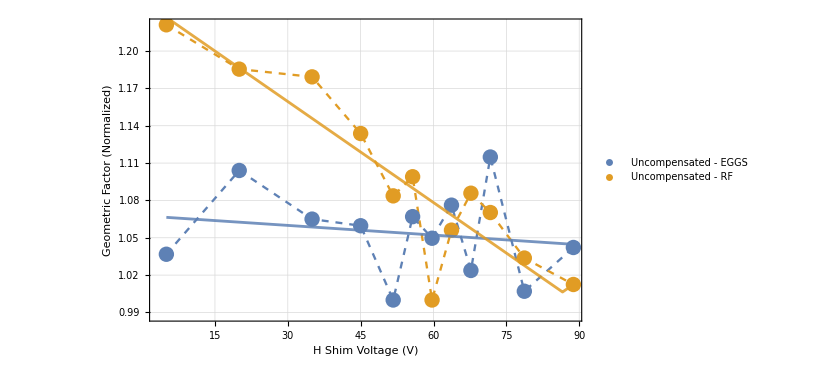

(-Graphics-
-Graphics-)

```mathematica
summaryQVSAFigure
Transpose[{summaryCH0CH1FigureEGGS,summaryCH0CH1FigureRF}]//MatrixForm
```

# 2025/08/13: QVSA Null vs Freq - RF Mode/H Shim (*todo: rename stuff*)

## Dadadada

```mathematica
(*todo; rename stuff for clarity*)
```

## Data Store

Dataset Structure: {
	{ion_pos_x, ion_pos_y}, {volt_vertical_shim, volt_horizontal_shim},
	{
		{att_RF_40MHz_raw, ampl_RF_40MHz_raw, nbar_RF_40MHz_raw},
		{att_RF_40MHz_ch0, ampl_RF_40MHz_ch0, nbar_RF_40MHz_ch0}, 
		{att_RF_40MHz_ch1, ampl_RF_40MHz_ch1, nbar_RF_40MHz_ch1},
	},
	{
		{att_RF_100MHz_raw, ampl_RF_100MHz_raw, nbar_RF_100MHz_raw},
		{att_RF_100MHz_ch0, ampl_RF_100MHz_ch0, nbar_RF_100MHz_ch0},
		{att_RF_100MHz_ch1, ampl_RF_100MHz_ch1, nbar_RF_100MHz_ch1}
	}
}

2025/08/13: qvsa strength (radial) at different radial positions - adjust H shim only (b/c visible on camera)

```mathematica
(*2025/08/13: radial qvsa strength vs H Shim - 40 MHz & 100 MHz*)
dataDJ={
{
{278,338},{71.6,5.},
{{31.5,7.,1.355},{30.,7.,0.514},{26.,7.,0.784}},
{{29.,12.,0.680},{20.,12.,0.810},{20.5,12.,0.844}}
},
{
{278,338},{71.6,10.},
{{28.,7.,0.885},{25.,7.,0.629},{23.,7.,1.111}},
{{31.5,12.,0.672},{20.,12.,0.630},{20.,12.,0.509}}
},
{
{278,337},{71.6,20.},
{{28.,7.,0.555},{27.,7.,0.581},{14.,7.,0.541}},
{{30.5,12.,0.484},{20.,12.,0.785},{19.,12.,0.833}}
},
{
{278,336},{71.6,30.0},
{{31.5,7.,0.800},{25.,7.,0.530},{25.,7.,0.365}},
{{31.5,12.,0.278},{23.,12.,0.341},{23.,12.,0.467}}
},
{
{278,335},{71.6,40.},
{{31.5,7.,0.900},{18.,7.,0.356},{26.,7.,0.973}},
{{31.5,12.,0.406},{23.,12.,0.378},{27.,12.,0.284}}
},
{
{278,335},{71.6,51.0},
{{31.5,7.,0.515},{25.,7.0,0.443},{30.,7.,0.457}},
{{31.5,12.,0.450},{23.,12.,0.681},{27.,12.,0.547}}
},
{
{278,334},{71.6,60.},
{{31.5,7.,0.403},{26.5,7.,0.667},{30.,7.,0.713}},
{{31.5,12.,0.471},{23.,12.,0.904},{27.,12.,0.841}}
},
{
{278,334},{71.6,70.0},
{{31.5,7.,0.344},{28.,7.,0.739},{31.5,7.,0.708}},
{{31.5,12.,0.505},{25.,12.,0.567},{28.5,12.,0.680}}
},
{
{278,334},{71.6,80.},
{{31.5,7.,0.369},{29.5,7.,0.775},{31.5,6.2,0.653}},
{{31.5,12.,0.480},{25.,12.,0.698},{29.5,12.,0.671}}
},
{
{278,332},{71.6,90.},
{{28.5,7.,0.593},{30.,7.,0.983},{31.5,6.,0.732}},
{{31.5,12.,0.557},{25.,12.,0.756},{29.5,12.,0.802}}
},
{
{278,331},{71.6,100.},
{{26.5,7.,0.744},{31.5,7.,0.638},{31.5,6.,0.891}},
{{31.,12.,0.721},{26.5,12.,0.460},{29.5,12.,0.805}}
},
{
{278,331},{71.6,110.},
{{25.5,7.,0.568},{31.5,7.,0.875},{31.5,6.,0.999}},
{{31.5,12.,0.552},{26.5,12.,0.540},{29.5,12.,1.056}}
}
};
```

## Data Select

```mathematica
(*collate dataset du jour*)
(*2025/08/13: radial qvsa strength vs H Shim - 40 MHz & 100 MHz*)
dataDJ={
{
{278,338},{71.6,5.},
{{31.5,7.,1.355},{30.,7.,0.514},{26.,7.,0.784}},
{{29.,12.,0.680},{20.,12.,0.810},{20.5,12.,0.844}}
},
{
{278,338},{71.6,10.},
{{28.,7.,0.885},{25.,7.,0.629},{23.,7.,1.111}},
{{31.5,12.,0.672},{20.,12.,0.630},{20.,12.,0.509}}
},
{
{278,337},{71.6,20.},
{{28.,7.,0.555},{27.,7.,0.581},{14.,7.,0.541}},
{{30.5,12.,0.484},{20.,12.,0.785},{19.,12.,0.833}}
},
{
{278,336},{71.6,30.0},
{{31.5,7.,0.800},{25.,7.,0.530},{25.,7.,0.365}},
{{31.5,12.,0.278},{23.,12.,0.341},{23.,12.,0.467}}
},
{
{278,335},{71.6,40.},
{{31.5,7.,0.900},{18.,7.,0.356},{26.,7.,0.973}},
{{31.5,12.,0.406},{23.,12.,0.378},{27.,12.,0.284}}
},
{
{278,335},{71.6,51.0},
{{31.5,7.,0.515},{25.,7.0,0.443},{30.,7.,0.457}},
{{31.5,12.,0.450},{23.,12.,0.681},{27.,12.,0.547}}
},
{
{278,334},{71.6,60.},
{{31.5,7.,0.403},{26.5,7.,0.667},{30.,7.,0.713}},
{{31.5,12.,0.471},{23.,12.,0.904},{27.,12.,0.841}}
},
{
{278,334},{71.6,70.0},
{{31.5,7.,0.344},{28.,7.,0.739},{31.5,7.,0.708}},
{{31.5,12.,0.505},{25.,12.,0.567},{28.5,12.,0.680}}
},
{
{278,334},{71.6,80.},
{{31.5,7.,0.369},{29.5,7.,0.775},{31.5,6.2,0.653}},
{{31.5,12.,0.480},{25.,12.,0.698},{29.5,12.,0.671}}
},
{
{278,332},{71.6,90.},
{{28.5,7.,0.593},{30.,7.,0.983},{31.5,6.,0.732}},
{{31.5,12.,0.557},{25.,12.,0.756},{29.5,12.,0.802}}
},
{
{278,331},{71.6,100.},
{{26.5,7.,0.744},{31.5,7.,0.638},{31.5,6.,0.891}},
{{31.,12.,0.721},{26.5,12.,0.460},{29.5,12.,0.805}}
},
{
{278,331},{71.6,110.},
{{25.5,7.,0.568},{31.5,7.,0.875},{31.5,6.,0.999}},
{{31.5,12.,0.552},{26.5,12.,0.540},{29.5,12.,1.056}}
}
};
```

## Process

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[2,2]]<#2[[2,2]]&];
posDJ=dataDJ[[;;,2,2]];
```

```mathematica
(*convert phonon/QVSA params to scaled voltage*)
phononDataDJEGGS=Apply[
fdj,
dataDJ[[;;,3,;;]],
{2}
]//Transpose;
phononDataDJRF=Apply[
fdj,
dataDJ[[;;,4,;;]],
{2}
]//Transpose;
```

```mathematica
(*process QVSA strength data*)
dataQVSANullEGGS=Transpose[{posDJ,phononDataDJEGGS[[1]]}];
dataQVSANullEGGS[[;;,2]]/=Min[dataQVSANullEGGS[[;;,2]]];
dataQVSANullRF=Transpose[{posDJ,phononDataDJRF[[1]]}];
dataQVSANullRF[[;;,2]]/=Min[dataQVSANullRF[[;;,2]]];
```

```mathematica
(*process CH0 vs CH1 ampl imbalance data*)
dataCH0AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[2]]}];
dataCH1AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[3]]}];
dataCH0AmplRF=Transpose[{posDJ,phononDataDJRF[[2]]}];
dataCH1AmplRF=Transpose[{posDJ,phononDataDJRF[[3]]}];
```

```mathematica
(*normalize to minimum of BOTH CH0 and CH1 vals instead of respectively*)
(*amplImbalanceNorm=Min[{phononDataDJEGGS[[2;;3]],phononDataDJRF[[2;;3]]}];*)
amplImbalanceNormEGGS=Min[phononDataDJEGGS[[2;;3]]];
amplImbalanceNormRF=Min[phononDataDJRF[[2;;3]]];
dataCH0AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH1AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH0AmplRF[[;;,2]]/=amplImbalanceNormRF;
dataCH1AmplRF[[;;,2]]/=amplImbalanceNormRF;
```

## Try Fit

## Prepare Fitting

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
];
]];
```

## Do Fits

```mathematica
(*fit QVSA field null to abs func*)
AbsoluteTiming[
fitQVSANullEGGS=FitAbsFunc[dataQVSANullEGGS];
]
AbsoluteTiming[
fitQVSANullRF=FitAbsFunc[dataQVSANullRF];
]
```

{0.0998731,Null}

{0.0081311,Null}

```mathematica
(*fit CH0/CH1 relative geometric factor to abs func*)
AbsoluteTiming[
fitCH0AmplEGGS=FitAbsFunc[dataCH0AmplEGGS];
fitCH1AmplEGGS=FitAbsFunc[dataCH1AmplEGGS];
]
AbsoluteTiming[
fitCH0AmplRF=FitAbsFunc[dataCH0AmplRF];
fitCH1AmplRF=FitAbsFunc[dataCH1AmplRF];
]
```

{0.0123098,Null}

{0.0100722,Null}

## Get Fit Params

```mathematica
(*get fit params*)
fitQVSAParamsEGGS=Style[
fitQVSANullEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitQVSAParamsRF=Style[
fitQVSANullRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsEGGS=Style[
fitCH0AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsEGGS=Style[
fitCH1AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsRF=Style[
fitCH0AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsRF=Style[
fitCH1AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

## QVSA Null

```mathematica
(*plot fitted results*)
fitQVSAPlot=Plot[
{fitQVSANullEGGS[x],fitQVSANullRF[x]},
{x,dataQVSANullRF[[1,1]],dataQVSANullRF[[-1,1]]},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.0033],Opacity[0.85]},
{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot qvsa null data*)
summaryQVSAFigure=Show[{
ListPlot[
{
dataQVSANullEGGS,dataQVSANullEGGS,
dataQVSANullRF,dataQVSANullRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["QVSA Field Null (Radial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.018]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},

PlotLegends->{
"Uncompensated - EGGS",None,
"Uncompensated - RF",None
},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitQVSAPlot
}];
```

## CH0 vs CH1 “Geometric Factor”

### EGGS mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotEGGS=Plot[
fitCH0AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[3]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotEGGS=Plot[
fitCH1AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[4]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureEGGS=Show[{
ListPlot[
{
dataCH0AmplEGGS,dataCH0AmplEGGS,
dataCH1AmplEGGS,dataCH1AmplEGGS
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[3]],PointSize[0.018]},
{DefaultPlotColors[[3]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[4]],PointSize[0.018]},
{DefaultPlotColors[[4]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - EGGS",None,
"CH1 - EGGS",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotEGGS,
fitCH1PlotEGGS
}];
```

### RF Mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotRF=Plot[
fitCH0AmplRF[x],
{x,dataCH0AmplRF[[1,1]],dataCH0AmplRF[[-1,1]]},
PlotStyle->{
DefaultPlotColors[[5]],Thickness[0.0033],Opacity[0.85]
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotRF=Plot[
fitCH1AmplRF[x],
{x,dataCH1AmplRF[[1,1]],dataCH1AmplRF[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[6]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureRF=Show[{
ListPlot[
{
dataCH0AmplRF,dataCH0AmplRF,
dataCH1AmplRF,dataCH1AmplRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[5]],PointSize[0.018]},
{DefaultPlotColors[[5]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[6]],PointSize[0.018]},
{DefaultPlotColors[[6]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - RF",None,
"CH1 - RF",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotRF,
fitCH1PlotRF
}];
```

## Show

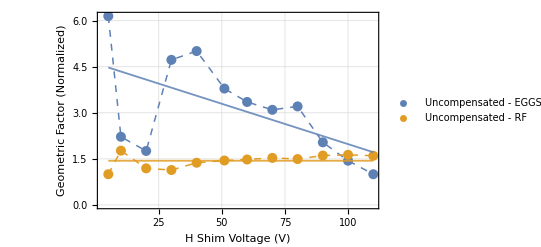

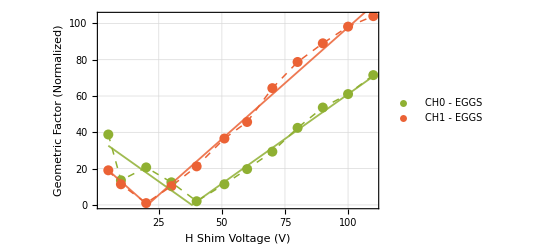
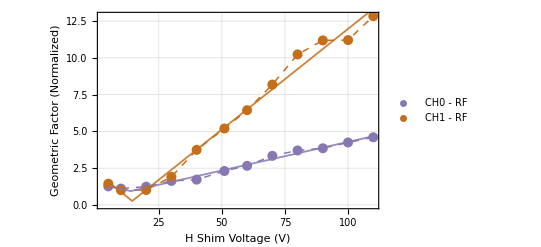
(-Graphics-
-Graphics-)

```mathematica
summaryQVSAFigure
Transpose[{summaryCH0CH1FigureEGGS,summaryCH0CH1FigureRF}]//MatrixForm
```

# 2025/08/14: QVSA Null vs Freq - Axial Mode/Endcaps

## Dadadada

## Data Store

Dataset Structure: {
	{ion_pos_x, ion_pos_y}, {volt_vertical_shim, volt_horizontal_shim},
	{
		{att_AX_40MHz_raw, ampl_AX_40MHz_raw, nbar_AX_40MHz_raw},
		{att_AX_40MHz_ch0, ampl_AX_40MHz_ch0, nbar_AX_40MHz_ch0}, 
		{att_AX_40MHz_ch1, ampl_AX_40MHz_ch1, nbar_AX_40MHz_ch1},
	},
	{
		{att_AX_100MHz_raw, ampl_AX_100MHz_raw, nbar_AX_100MHz_raw},
		{att_AX_100MHz_ch0, ampl_AX_100MHz_ch0, nbar_AX_100MHz_ch0},
		{att_AX_100MHz_ch1, ampl_AX_100MHz_ch1, nbar_AX_100MHz_ch1}
	}
}

2025/08/14: qvsa strength (radial) at different radial positions - adjust H shim only (b/c visible on camera)

```mathematica
(*2025/08/14: radial qvsa strength vs H Shim - 40 MHz & 100 MHz*)
dataDJ={
{
{278,338},{71.6,5.},
{{31.5,7.,1.355},{30.,7.,0.514},{26.,7.,0.784}},
{{29.,12.,0.680},{20.,12.,0.810},{20.5,12.,0.844}}
},
{
{278,338},{71.6,10.},
{{28.,7.,0.885},{25.,7.,0.629},{23.,7.,1.111}},
{{31.5,12.,0.672},{20.,12.,0.630},{20.,12.,0.509}}
},
{
{278,337},{71.6,20.},
{{28.,7.,0.555},{27.,7.,0.581},{14.,7.,0.541}},
{{30.5,12.,0.484},{20.,12.,0.785},{19.,12.,0.833}}
},
{
{278,336},{71.6,30.0},
{{31.5,7.,0.800},{25.,7.,0.530},{25.,7.,0.365}},
{{31.5,12.,0.278},{23.,12.,0.341},{23.,12.,0.467}}
},
{
{278,335},{71.6,40.},
{{31.5,7.,0.900},{18.,7.,0.356},{26.,7.,0.973}},
{{31.5,12.,0.406},{23.,12.,0.378},{27.,12.,0.284}}
},
{
{278,335},{71.6,51.0},
{{31.5,7.,0.515},{25.,7.0,0.443},{30.,7.,0.457}},
{{31.5,12.,0.450},{23.,12.,0.681},{27.,12.,0.547}}
},
{
{278,334},{71.6,60.},
{{31.5,7.,0.403},{26.5,7.,0.667},{30.,7.,0.713}},
{{31.5,12.,0.471},{23.,12.,0.904},{27.,12.,0.841}}
},
{
{278,334},{71.6,70.0},
{{31.5,7.,0.344},{28.,7.,0.739},{31.5,7.,0.708}},
{{31.5,12.,0.505},{25.,12.,0.567},{28.5,12.,0.680}}
},
{
{278,334},{71.6,80.},
{{31.5,7.,0.369},{29.5,7.,0.775},{31.5,6.2,0.653}},
{{31.5,12.,0.480},{25.,12.,0.698},{29.5,12.,0.671}}
},
{
{278,332},{71.6,90.},
{{28.5,7.,0.593},{30.,7.,0.983},{31.5,6.,0.732}},
{{31.5,12.,0.557},{25.,12.,0.756},{29.5,12.,0.802}}
},
{
{278,331},{71.6,100.},
{{26.5,7.,0.744},{31.5,7.,0.638},{31.5,6.,0.891}},
{{31.,12.,0.721},{26.5,12.,0.460},{29.5,12.,0.805}}
},
{
{278,331},{71.6,110.},
{{25.5,7.,0.568},{31.5,7.,0.875},{31.5,6.,0.999}},
{{31.5,12.,0.552},{26.5,12.,0.540},{29.5,12.,1.056}}
}
};
```

## Data Select

```mathematica
(*collate dataset du jour*)
(*2025/08/13: radial qvsa strength vs H Shim - 40 MHz & 100 MHz*)
dataDJ={
{
{278,338},{71.6,5.},
{{31.5,7.,1.355},{30.,7.,0.514},{26.,7.,0.784}},
{{29.,12.,0.680},{20.,12.,0.810},{20.5,12.,0.844}}
},
{
{278,338},{71.6,10.},
{{28.,7.,0.885},{25.,7.,0.629},{23.,7.,1.111}},
{{31.5,12.,0.672},{20.,12.,0.630},{20.,12.,0.509}}
},
{
{278,337},{71.6,20.},
{{28.,7.,0.555},{27.,7.,0.581},{14.,7.,0.541}},
{{30.5,12.,0.484},{20.,12.,0.785},{19.,12.,0.833}}
},
{
{278,336},{71.6,30.0},
{{31.5,7.,0.800},{25.,7.,0.530},{25.,7.,0.365}},
{{31.5,12.,0.278},{23.,12.,0.341},{23.,12.,0.467}}
},
{
{278,335},{71.6,40.},
{{31.5,7.,0.900},{18.,7.,0.356},{26.,7.,0.973}},
{{31.5,12.,0.406},{23.,12.,0.378},{27.,12.,0.284}}
},
{
{278,335},{71.6,51.0},
{{31.5,7.,0.515},{25.,7.0,0.443},{30.,7.,0.457}},
{{31.5,12.,0.450},{23.,12.,0.681},{27.,12.,0.547}}
},
{
{278,334},{71.6,60.},
{{31.5,7.,0.403},{26.5,7.,0.667},{30.,7.,0.713}},
{{31.5,12.,0.471},{23.,12.,0.904},{27.,12.,0.841}}
},
{
{278,334},{71.6,70.0},
{{31.5,7.,0.344},{28.,7.,0.739},{31.5,7.,0.708}},
{{31.5,12.,0.505},{25.,12.,0.567},{28.5,12.,0.680}}
},
{
{278,334},{71.6,80.},
{{31.5,7.,0.369},{29.5,7.,0.775},{31.5,6.2,0.653}},
{{31.5,12.,0.480},{25.,12.,0.698},{29.5,12.,0.671}}
},
{
{278,332},{71.6,90.},
{{28.5,7.,0.593},{30.,7.,0.983},{31.5,6.,0.732}},
{{31.5,12.,0.557},{25.,12.,0.756},{29.5,12.,0.802}}
},
{
{278,331},{71.6,100.},
{{26.5,7.,0.744},{31.5,7.,0.638},{31.5,6.,0.891}},
{{31.,12.,0.721},{26.5,12.,0.460},{29.5,12.,0.805}}
},
{
{278,331},{71.6,110.},
{{25.5,7.,0.568},{31.5,7.,0.875},{31.5,6.,0.999}},
{{31.5,12.,0.552},{26.5,12.,0.540},{29.5,12.,1.056}}
}
};
```

## Process

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[2,2]]<#2[[2,2]]&];
posDJ=dataDJ[[;;,2,2]];
```

```mathematica
(*convert phonon/QVSA params to scaled voltage*)
phononDataDJEGGS=Apply[
fdj,
dataDJ[[;;,3,;;]],
{2}
]//Transpose;
phononDataDJRF=Apply[
fdj,
dataDJ[[;;,4,;;]],
{2}
]//Transpose;
```

```mathematica
(*process QVSA strength data*)
dataQVSANullEGGS=Transpose[{posDJ,phononDataDJEGGS[[1]]}];
dataQVSANullEGGS[[;;,2]]/=Min[dataQVSANullEGGS[[;;,2]]];
dataQVSANullRF=Transpose[{posDJ,phononDataDJRF[[1]]}];
dataQVSANullRF[[;;,2]]/=Min[dataQVSANullRF[[;;,2]]];
```

```mathematica
(*process CH0 vs CH1 ampl imbalance data*)
dataCH0AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[2]]}];
dataCH1AmplEGGS=Transpose[{posDJ,phononDataDJEGGS[[3]]}];
dataCH0AmplRF=Transpose[{posDJ,phononDataDJRF[[2]]}];
dataCH1AmplRF=Transpose[{posDJ,phononDataDJRF[[3]]}];
```

```mathematica
(*normalize to minimum of BOTH CH0 and CH1 vals instead of respectively*)
(*amplImbalanceNorm=Min[{phononDataDJEGGS[[2;;3]],phononDataDJRF[[2;;3]]}];*)
amplImbalanceNormEGGS=Min[phononDataDJEGGS[[2;;3]]];
amplImbalanceNormRF=Min[phononDataDJRF[[2;;3]]];
dataCH0AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH1AmplEGGS[[;;,2]]/=amplImbalanceNormEGGS;
dataCH0AmplRF[[;;,2]]/=amplImbalanceNormRF;
dataCH1AmplRF[[;;,2]]/=amplImbalanceNormRF;
```

## Try Fit

## Prepare Fitting

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
];
]];
```

## Do Fits

```mathematica
(*fit QVSA field null to abs func*)
AbsoluteTiming[
fitQVSANullEGGS=FitAbsFunc[dataQVSANullEGGS];
]
AbsoluteTiming[
fitQVSANullRF=FitAbsFunc[dataQVSANullRF];
]
```

{0.0998731,Null}

{0.0081311,Null}

```mathematica
(*fit CH0/CH1 relative geometric factor to abs func*)
AbsoluteTiming[
fitCH0AmplEGGS=FitAbsFunc[dataCH0AmplEGGS];
fitCH1AmplEGGS=FitAbsFunc[dataCH1AmplEGGS];
]
AbsoluteTiming[
fitCH0AmplRF=FitAbsFunc[dataCH0AmplRF];
fitCH1AmplRF=FitAbsFunc[dataCH1AmplRF];
]
```

{0.0123098,Null}

{0.0100722,Null}

## Get Fit Params

```mathematica
(*get fit params*)
fitQVSAParamsEGGS=Style[
fitQVSANullEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitQVSAParamsRF=Style[
fitQVSANullRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsEGGS=Style[
fitCH0AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsEGGS=Style[
fitCH1AmplEGGS["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*get fit params*)
fitCH0ParamsRF=Style[
fitCH0AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
fitCH1ParamsRF=Style[
fitCH1AmplRF["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

## QVSA Null

```mathematica
(*plot fitted results*)
fitQVSAPlot=Plot[
{fitQVSANullEGGS[x],fitQVSANullRF[x]},
{x,dataQVSANullRF[[1,1]],dataQVSANullRF[[-1,1]]},

PlotStyle->{
{DefaultPlotColors[[1]],Thickness[0.0033],Opacity[0.85]},
{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot qvsa null data*)
summaryQVSAFigure=Show[{
ListPlot[
{
dataQVSANullEGGS,dataQVSANullEGGS,
dataQVSANullRF,dataQVSANullRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["QVSA Field Null (Radial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.018]},
{DefaultPlotColors[[1]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},

PlotLegends->{
"Uncompensated - EGGS",None,
"Uncompensated - RF",None
},

ImageSize->Scaled[0.31]
],

(*combine with fitted plot*)
fitQVSAPlot
}];
```

## CH0 vs CH1 “Geometric Factor”

### EGGS mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotEGGS=Plot[
fitCH0AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[3]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotEGGS=Plot[
fitCH1AmplEGGS[x],
{x,dataCH0AmplEGGS[[1,1]],dataCH0AmplEGGS[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[4]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureEGGS=Show[{
ListPlot[
{
dataCH0AmplEGGS,dataCH0AmplEGGS,
dataCH1AmplEGGS,dataCH1AmplEGGS
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[3]],PointSize[0.018]},
{DefaultPlotColors[[3]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[4]],PointSize[0.018]},
{DefaultPlotColors[[4]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - EGGS",None,
"CH1 - EGGS",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotEGGS,
fitCH1PlotEGGS
}];
```

### RF Mode

```mathematica
(*plot fitted results - CH0*)
fitCH0PlotRF=Plot[
fitCH0AmplRF[x],
{x,dataCH0AmplRF[[1,1]],dataCH0AmplRF[[-1,1]]},
PlotStyle->{
DefaultPlotColors[[5]],Thickness[0.0033],Opacity[0.85]
}
];
```

```mathematica
(*plot fitted results - CH1*)
fitCH1PlotRF=Plot[
fitCH1AmplRF[x],
{x,dataCH1AmplRF[[1,1]],dataCH1AmplRF[[-1,1]]},
PlotStyle->{
{DefaultPlotColors[[6]],Thickness[0.0033],Opacity[0.85]}
}
];
```

```mathematica
(*plot CH0/CH1 ampl data*)
summaryCH0CH1FigureRF=Show[{
ListPlot[
{
dataCH0AmplRF,dataCH0AmplRF,
dataCH1AmplRF,dataCH1AmplRF
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Geometric Factor (Normalized)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Relative CH0 vs CH1 QVSA Strength",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[5]],PointSize[0.018]},
{DefaultPlotColors[[5]],Dashed,Thickness[0.0027]},

{DefaultPlotColors[[6]],PointSize[0.018]},
{DefaultPlotColors[[6]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True
},
PlotLegends->{
"CH0 - RF",None,
"CH1 - RF",None
},

ImageSize->Scaled[0.45]
],

(*combine with fitted plot*)
fitCH0PlotRF,
fitCH1PlotRF
}];
```

## Show

```mathematica
summaryQVSAFigure
Transpose[{summaryCH0CH1FigureEGGS,summaryCH0CH1FigureRF}]//MatrixForm
```

-Graphics-

(-Graphics-
-Graphics-)

# 2025/10/17: Axial Shimming After Warmup

## Dadadada

## Data Store

Dataset Structure: {
	{ion_pos_x,ion_pos_y}, {volt_east_endcap, volt_west_endcap}, {xum_rabi_ratio},
}

```mathematica
(*collate dataset du jour*)
dataDJ20250809={
{{238,335},{182,343},{1./13.43}},
{{255,335},{190,330},{1./24.39}},
{{282,337},{205,308},{1./14.84}},
{{283,336},{205,308},{1./22.50}},
{{306,337},{217,290},{1./10.90}},
{{319,338},{224,282},{1./13.17}},
{{330,337},{231,275},{1./8.18}},
{{351,339},{243,261},{1./5.05}},
{{362,339},{250,254},{1./4.96}},
{{383,340},{263,242},{1./3.95}}
};
```

## Data Select

```mathematica
dataDJ={
{{198,338},{174,357},{1./21.10}},
{{206,337},{178,350},{1./100.93}},
{{210,337},{180,346},{1./74.34}},
{{214,338},{182,343},{1./117.12}},
{{230,338},{190,331},{1./25.34}},
{{246,339},{198,319},{1./11.31}}
(*{{282,337},{205,308},{1./14.84}},
{{306,337},{217,290},{1./10.90}},
{{319,338},{224,282},{1./13.17}}*)
};
```

## Process All

## Process Data

```mathematica
(*sort data and prepare general*)
dataDJ=Sort[dataDJ,#1[[1,1]]<#2[[1,1]]&];
posDJ=dataDJ[[;;,1,1]];
```

```mathematica
(*process xum null data*)
dataXUMNull=Transpose[{posDJ,dataDJ[[;;,3,1]]}];
```

## Prepare Fit Function

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x
]
];
]];
```

## Do Fits

```mathematica
(*fit xum field null to abs func*)
AbsoluteTiming[
fitXUMNull=FitAbsFunc[dataXUMNull];
];
```

```mathematica
(*get fit params*)
fitXUMParams=Style[
fitXUMNull["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted results*)
fitXUMPlot=Plot[
fitXUMNull[x],
{x,dataXUMNull[[1,1]],dataXUMNull[[-1,1]]},
PlotStyle->{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
];
```

```mathematica
(*plot trap xum null data*)
summaryXUMFigure=Show[{
ListPlot[
{dataXUMNull,dataXUMNull},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{ 
{Style["Micromotion Index (β)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["Trap RF Field Null (Axial)",{Black,Directive[15]}]
}
},
PlotStyle->{
{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True,
False,True
},
PlotLegends->{"XUM Null",None},

ImageSize->Scaled[0.51]
],

(*combine with fitted plot*)
fitXUMPlot
}];
```

## Show

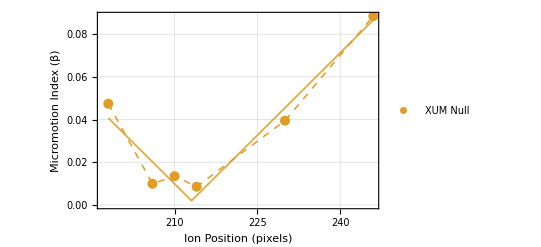
( | Estimate | Standard Error | Confidence Interval
Ampl | 0.00257128 | 0.000353036 | {0.00144776,0.00369479}
x0 | 213.077 | 1.47809 | {208.373,217.781}
C0 | 0.00196717 | 0.00567304 | {-0.016087,0.0200213}
-Graphics-)

```mathematica
{fitXUMParams,summaryXUMFigure}//MatrixForm
```